```mathematica
IX1303
Inlämningsuppgift Mathematica

Muttakin Kairm, TIEDB

Följande rapport består av 9 uppgifter.Uppgiftnummer från häftet:1,2,3,5,6,8,13,18,20.
```

```mathematica
1.
-Graphics-
```

```mathematica
RegionPlot3D[z>=√(x^2+y^2), {x, -5, 5}, {y, -5, 5}, {z, -5, 5}, AxesLabel->{x,y,z}, Mesh->None]
```

-Graphics3D-

```mathematica
Från grafen kan man analysera att ekvationen ger ett konformigt föremål med lösnings mängde: -x<=solx<=x, -y<=soly<=y och 0<=solz<=z
```

```mathematica
Clear["Global`*"]
```

```mathematica
2.

-Graphics-
𝒂=2𝒊+𝒋−2𝒌  and  𝒃=3𝒊−2𝒋−𝒌 . För att ta fram vinkeln mellan vektorer a och b, den följande ekvation har använts:
cos(θ) = (a.b)/(|a||b|)=((2)(3)+(1)(-2)+(-2)(-1))/((√((2)^2+(1)^2+(-2)^2))(√((3)^2+(-2)^2+(-1)^2)))=6/((√9)(√14))=2/(√14)=√(2/7)
```

```mathematica
VectorAngle[{2,1,-2},{3,-2,-1}]
```

ArcCos[√(2/7)]

```mathematica
Graphics3D[{Thick,Line[{{0,0,0},{2,1,-2}}],Line[{{0,0,0},{3,-2,-1}}]}, ViewAngle->Automatic]
```

-Graphics3D-

```mathematica
Manuell användning av formel ger cosθ√(2/7). När man sätter upp vektorer i Mathematica med kommandot VectorAngle får man också samma svar. Kommandot Graphics 3D jälper att rita en skalenlig figur som visar vinkeln mellan två givna vektorer. Från grafen kan man anta att vinkeln ligger mellan noll och 90 grader. Om man löser cosθ får man 57.7 grader som stämmer enligt grafen.
```

```mathematica
Clear["Global`*"]
```

```mathematica
3.
```

```mathematica
Solve[{x+2y+3z==1,2x+4y+7z==2,3x+7y+11z==8},{x,y,z}]
```

{{x→-9,y→5,z→0}}

```mathematica
Show[ContourPlot3D[{x+2y+3z==1,2x+4y+7z==2,3x+7y+11z==8}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, AxesLabel->{"x","y","z"},Mesh->None,ContourStyle->Directive[Green,Opacity[0.2]]],Graphics3D[{Red, PointSize[0.03],Point[{-9,5,0}]}]]
```

-Graphics3D-

```mathematica
Först,Solve funktionen har använts att ta fram algebraisk lösning till ekvationer och deras skär punkt. Från grafen ovanför kan man analysera de  planen som var skapat med hjälp av ContourPlot3D. Med användning av Graphics3D och lösningar till ekvationer  hjälpte att visa skär punkten med en röd punkt på grafen.
```

```mathematica
Clear["Global`*"]
```

```mathematica
5.
```

```mathematica
Solve[{x-2y==2,3x+5y==17},{x,y}]
```

{{x→4,y→1}}

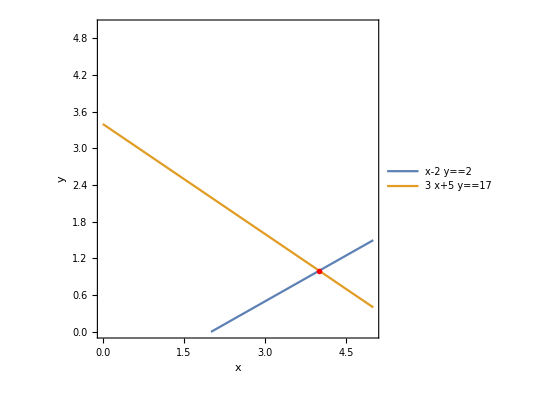

```mathematica
ContourPlot[{x-2y==2,3x+5y==17},{x,0,5},{y,0,5},AxesLabel->{"x","y"}, Epilog-> {Red, PointSize[0.01],Point[{4,1}]}, PlotLegends->LineLegend["Expressions"]]
```

```mathematica
När man plottar de två ekvationer ser man att det finns en lösning. Grafen ovän var plottade med ContourPlot och den Epilog funktionen hjälpte att sätta skär punkten. Ekvation system var också löste med hjälp av vänlig Solve metod. I sin helhet kan man se att ekvationssystemet har en grafisk lösning.
```

```mathematica
Clear["Global`*"]
```

```mathematica
6.
```

```mathematica
Show[ContourPlot3D[{3x+4y+-z==8,6x+8y-2z==3}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, AxesLabel->{"x","y","z"},Mesh->None,ContourStyle->Directive[Purple,Opacity[0.2]]]]
```

```mathematica
-Graphics3D-
Från grafen ovanför kan man se att ekvationer är parallella och har ingen gemensam punkt.Därför systemet saknar lösning.
```

```mathematica
Clear["Global`*"]
```

```mathematica
8.
```

```mathematica
MatrixForm[M1 = {{2,4,8},{4,5,1},{7,9,3}}]
```

(2 | 4 | 8
4 | 5 | 1
7 | 9 | 3)

```mathematica
RowReduce[M1]//MatrixForm
```

(1 | 0 | -6
0 | 1 | 5
0 | 0 | 0)

```mathematica
Funktionerna MatrixForm och RowReduce hjälpte att ta fram rref av givna matrisen. På den sista rad kan man se att alla värden är noll. Det betyder att en av dem ekvationerna är redundant och matrisen har oändliga lösningar.
```

```mathematica
Clear["Global`*"]
```

## 13. -Graphics-

```mathematica
a = {{.1588,.0064,.0025,.0304,.0014,.0083,.1594},{.0057,.2645,.0436,.0099,.0083,.0201,.3413},{.0264,.1506,.3557,.0139,.0142,.0070,.0236}, {.3299,.0565,.0495,.3636,.0204,.0483,.0649}, {.0089,.0081,.0333,.0295,.3412,.0237,.0020}, {.1190,.0901,.0996,.1260,.1722,.2368,.3369}, {.0063,.0126,.0196,.0098,.0064,.0132,.0012}}
```

{{0.1588,0.0064,0.0025,0.0304,0.0014,0.0083,0.1594},{0.0057,0.2645,0.0436,0.0099,0.0083,0.0201,0.3413},{0.0264,0.1506,0.3557,0.0139,0.0142,0.007,0.0236},{0.3299,0.0565,0.0495,0.3636,0.0204,0.0483,0.0649},{0.0089,0.0081,0.0333,0.0295,0.3412,0.0237,0.002},{0.119,0.0901,0.0996,0.126,0.1722,0.2368,0.3369},{0.0063,0.0126,0.0196,0.0098,0.0064,0.0132,0.0012}}

```mathematica
IA= IdentityMatrix[7]-a
```

{{0.8412,-0.0064,-0.0025,-0.0304,-0.0014,-0.0083,-0.1594},{-0.0057,0.7355,-0.0436,-0.0099,-0.0083,-0.0201,-0.3413},{-0.0264,-0.1506,0.6443,-0.0139,-0.0142,-0.007,-0.0236},{-0.3299,-0.0565,-0.0495,0.6364,-0.0204,-0.0483,-0.0649},{-0.0089,-0.0081,-0.0333,-0.0295,0.6588,-0.0237,-0.002},{-0.119,-0.0901,-0.0996,-0.126,-0.1722,0.7632,-0.3369},{-0.0063,-0.0126,-0.0196,-0.0098,-0.0064,-0.0132,0.9988}}

```mathematica
invIA=Inverse[IA]
```

{{1.22119,0.0270856,0.0225685,0.0677001,0.0135465,0.0226551,0.216748},{0.0432427,1.40455,0.124385,0.0465836,0.0403637,0.0516298,0.510313},{0.0805574,0.338749,1.59274,0.0555055,0.0507739,0.0326252,0.180957},{0.673244,0.190455,0.176277,1.64481,0.094835,0.126639,0.326472},{0.0635781,0.0531293,0.100977,0.0897173,1.53928,0.057515,0.0589992},{0.340947,0.271065,0.295271,0.325295,0.384174,1.36736,0.637139},{0.0213481,0.0303284,0.0392457,0.0231163,0.0174619,0.0211164,1.02456}}

```mathematica
d ={{74000},{56000},{10500}, {25000},{17500}, {196000}, {5000}}
```

{{74000},{56000},{10500},{25000},{17500},{196000},{5000}}

```mathematica
X=MatrixForm[invIA.d]
```

(99575.7
97703.
51230.5
131570.
49488.5
329554.
13835.3)

```mathematica
Production levels (in millions of dollars) needed to satisfy the final demand
1. nonmetal household and personal products:99575.7
2. final metal products (such as motor vehicles):97703
3. basic metal products and mining:51230.5
4. basic nonmetal products and agriculture:131570
5. energy:49488.5
6. services:329554
7. entertainment and miscellaneous products:13835.3
```

```mathematica
Clear["Global`*"]
```

```mathematica
18.
```

```mathematica
MatrixForm[b1 ={{1, 1,1},{1,2,2},{1,2,3}}]
```

(1 | 1 | 1
1 | 2 | 2
1 | 2 | 3)

```mathematica
detb1= Det[b1]
```

1

```mathematica
MatrixForm[b2 ={{1,1,1,1},{1,2,2,2},{1,2,3,3},{1,2,3,4}}]
```

(1 | 1 | 1 | 1
1 | 2 | 2 | 2
1 | 2 | 3 | 3
1 | 2 | 3 | 4)

```mathematica
detb2=Det[b2]
```

1

```mathematica
MatrixForm[b3 = {{1,1,1,1,1},{1,2,2,2,2},{1,2,3,3,3},{1,2,3,4,4},{1,2,3,4,5}}]
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
1 | 2 | 3 | 3 | 3
1 | 2 | 3 | 4 | 4
1 | 2 | 3 | 4 | 5)

```mathematica
detb3=Det[b3]
```

1

```mathematica
MatrixForm[M= {{1,1,1,x,1},{1,2,2,x,2},{1,2,3,x,3},{x,x,x,x,x},{1,2,3,x,n}}]
```

(1 | 1 | 1 | x | 1
1 | 2 | 2 | x | 2
1 | 2 | 3 | x | 3
x | x | x | x | x
1 | 2 | 3 | x | n)

```mathematica
By finding the determinants of b1, b2, b3 which is equal to 1, an assumption can be made that Determinant of M=1. 
In order to prove this matrix M can be row reduced.
```

```mathematica
RowReduce[({{1, 1, 1, x, 1}, {1, 2, 2, x, 2}, {1, 2, 3, x, 3}, {x, x, x, x, x}, {1, 2, 3, x, n}})]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
This final matrix becomes an upper triangular matrix, determinant 1. Therefore, earlier assumption is right.
```

```mathematica
Clear["Global`*"]
```

```mathematica
20.
```

```mathematica
MatrixForm[x1={-10,2,-6,16,2}]
```

(-10
2
-6
16
2)

```mathematica
MatrixForm[x2={13,1,3,-16,1}]
```

(13
1
3
-16
1)

```mathematica
MatrixForm[x3={7,-5,13,-2,-5}]
```

(7
-5
13
-2
-5)

```mathematica
MatrixForm[x4={-11,3,-3,5,-7}]
```

(-11
3
-3
5
-7)

```mathematica
MatrixForm[v1=x1]
```

(-10
2
-6
16
2)

```mathematica
MatrixForm[v2=x2-((x2.v1)/(v1.v1)*v1)]
```

(3
3
-3
0
3)

```mathematica
MatrixForm[v3=x3-((x3.v1)/(v1.v1)*v1)-((x3.v2)/(v2.v2)*v2)]
```

(6
0
6
6
0)

```mathematica
MatrixForm[v4=x4-((x4.v1)/(v1.v1)*v1)-((x4.v2)/(v2.v2)*v2)-((x4.v3)/(v3.v3)*v3)]
```

(0
5
0
0
-5)

```mathematica
Orthogonal basis ={({{-10}, {2}, {-6}, {16}, {2}}),({{3}, {3}, {-3}, {0}, {3}}),({{6}, {0}, {6}, {6}, {0}}),({{0}, {5}, {0}, {0}, {-5}})}
```

```mathematica
Clear["Global`*"]
```